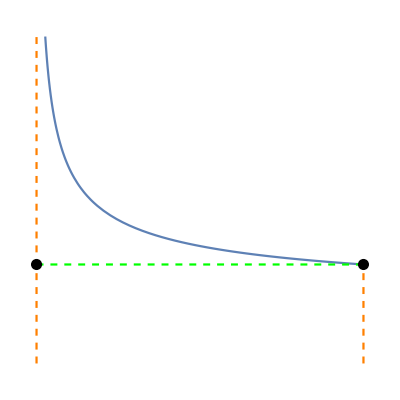

```mathematica
fx=Function[x,1/(x-0.5)^0.5+1];
f1=Plot[fx[x],{x,0.54,2},AxesOrigin-> {0,0},PlotRange-> All,AspectRatio->1,Epilog->{Disk[{2,fx[2]},Offset[4]],Disk[{0.5,fx[2]},Offset[4]]},Axes->False];
f2=ContourPlot[x==0.5,{x,0,1},{y,0,fx[0.54]},ContourStyle->{Orange,Dashed}];
f3=ContourPlot[x==2,{x,1,3},{y,0,fx[2]},ContourStyle->{Orange,Dashed}];
f4=Plot[fx[2],{x,0.5,2},PlotStyle->{Green,Dashed}];
Show[f1,f2,f3,f4]
```

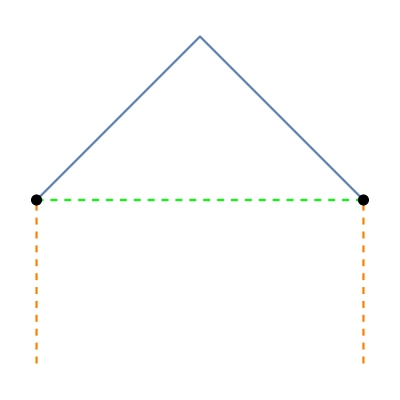

```mathematica
fx=Function[x,2-Abs[x-2]];
f1=Plot[fx[x],{x,1,3},AxesOrigin-> {0,0},PlotRange-> All,AspectRatio->1,Epilog->{Disk[{1,fx[1]},Offset[4]],Disk[{3,fx[3]},Offset[4]]},Axes->False];
f2=ContourPlot[x==1,{x,0,2},{y,0,fx[1]},ContourStyle->{Orange,Dashed}];
f3=ContourPlot[x==3,{x,2,4},{y,0,fx[3]},ContourStyle->{Orange,Dashed}];
f4=Plot[fx[3],{x,1,3},PlotStyle->{Green,Dashed}];
Show[f1,f2,f3,f4]
```

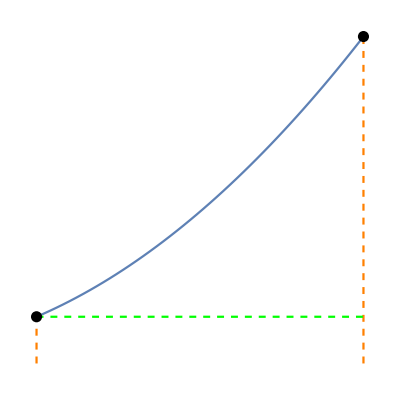

```mathematica
fx=Function[x,3x^2+1];
f1=Plot[fx[x],{x,1,3},AxesOrigin-> {0,0},PlotRange-> All,AspectRatio->1,Epilog->{Disk[{1,fx[1]},Offset[4]],Disk[{3,fx[3]},Offset[4]]},Axes->False];
f2=ContourPlot[x==1,{x,0,2},{y,0,fx[1]},ContourStyle->{Orange,Dashed}];
f3=ContourPlot[x==3,{x,2,4},{y,0,fx[3]},ContourStyle->{Orange,Dashed}];
f4=Plot[fx[1],{x,1,3},PlotStyle->{Green,Dashed}];
Show[f1,f2,f3,f4]
```

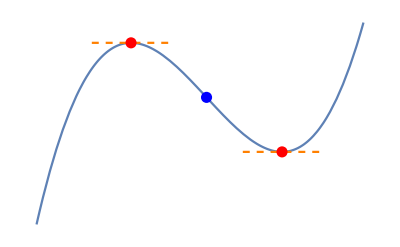

```mathematica
f2x=Function[x,(x-1)(x-2)(x-3)];
df2x=Function[x,D[f2x[x],x]];
df=Solve[df2x[x]==0,x];
d1=x/.df[[1]];
d2=x/.df[[2]];
ddf2x=Function[x,D[df2x[x],x]];
ddf=Solve[ddf2x[x]==0,x];
dd=x/.ddf[[1]];
p1=Plot[f2x[x],{x,0.7,3.2},Epilog-> {Red,Disk[{d1,f2x[d1]},Offset[4]],Disk[{d2,f2x[d2]},Offset[4]],Blue,Disk[{2,f2x[2]},Offset[4]]},Axes->False];
p2=Plot[f2x[d1],{x,d1-0.3,d1+0.3},PlotStyle->{Orange,Dashed}];
p3=Plot[f2x[d2],{x,d2-0.3,d2+0.3},PlotStyle->{Orange,Dashed}];
Show[p1,p2,p3]
```

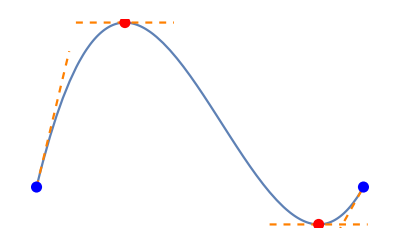

```mathematica
f2x=Function[x,(x-1)(x-2.4)(x-3)];
df2x=Function[x,D[f2x[x],x]];
k1=df2x[x]/.x-> 1;
k3=df2x[x]/.x-> 3;
df=Solve[df2x[x]==0,x];
d1=x/.df[[1]];
d2=x/.df[[2]];
ddf2x=Function[x,D[df2x[x],x]];
ddf=Solve[ddf2x[x]==0,x];
dd=x/.ddf[[1]];
p1=Plot[f2x[x],{x,1,3},Epilog-> {Red,Disk[{d1,f2x[d1]},Offset[4]],Disk[{d2,f2x[d2]},Offset[4]],Blue,
Disk[{1,f2x[1]},Offset[4]],Disk[{3,f2x[3]},Offset[4]]},Axes->False];
p2=Plot[f2x[d1],{x,d1-0.3,d1+0.3},PlotStyle->{Orange,Dashed}];
p3=Plot[f2x[d2],{x,d2-0.3,d2+0.3},PlotStyle->{Orange,Dashed}];
p4=Plot[f2x[1]+k1(x-1),{x,1,1.2},PlotStyle->{Orange,Dashed}];
p5=Plot[f2x[3]+k3(x-3),{x,2.8,3},PlotStyle->{Orange,Dashed}];
Show[p1,p2,p3,p4,p5]
```

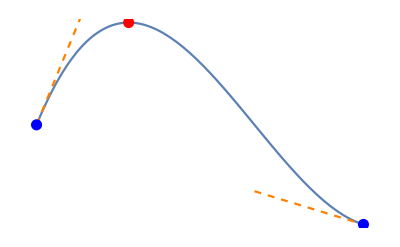

```mathematica
f3=Function[x,(x-1)(x-2)(x-3)];
df3=Function[x,D[f3[x],x]];
ddf3=Function[x,D[df3[x],x]];
sol=Solve[df3[x]==0,x];
rd1=x/.sol[[1]];
sol=Solve[ddf3[x]==0,x];
rdd=x/.sol[[1]];
p1=Plot[f3[x],{x,1,2.5},Epilog-> {Blue,Disk[{1,f3[1]},Offset[4]],Disk[{2.5,f3[2.5]},Offset[4]],Red,Disk[{rd1,f3[rd1]},Offset[4]]},Axes->False];
k1=df3[x]/.x->1;
k2=df3[x]/.x->2.5;
p2=Plot[k1*(x-1)+f3[1],{x,1,1.2},PlotStyle->{Orange,Dashed}];
p3=Plot[k2*(x-2.5)+f3[2.5],{x,2.,2.5},PlotStyle->{Orange,Dashed}];
p4=ContourPlot[x==rd1,{x,1,2},{y,0,f3[rd1]},ContourStyle->{Gray,Dashed}];
p5=ContourPlot[x==2.5,{x,2,3},{y,0,f3[2.5]},ContourStyle->{Gray,Dashed}];
Show[p1,p2,p3]
```

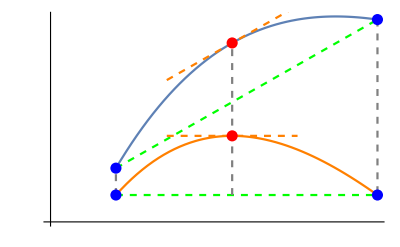

```mathematica
f2x=Function[x,(x-1)(x-2.6)^3(x-3)+0.2];
k=(f2x[1.4]-f2x[1])/0.4;
df2x=Function[x,D[f2x[x],x]];
df=Solve[df2x[x]==k,x];
d1=x/.df[[1]];
p1=Plot[f2x[x],{x,1,1.4},Epilog-> {Blue,Disk[{1,f2x[1]},Offset[4]],Disk[{1.4,f2x[1.4]},Offset[4]],Disk[{1,0},Offset[4]],Disk[{1.4,0},Offset[4]],Red,Disk[{d1,f2x[d1]},Offset[4]],Disk[{d1,f2x[d1]-k(d1-1)-0.2},Offset[4]]},AxesOrigin->{0.9,-0.2},AxesStyle->Directive[LightGray],Ticks->None];
p2=Plot[k(x-d1)+f2x[d1],{x,d1-0.1,d1+0.1},PlotStyle->{Orange,Dashed}];
p3=Plot[f2x[x]-k(x-1)-0.2,{x,1,1.4},PlotStyle->Orange];
p4=Plot[k*(x-1)+f2x[1],{x,1,1.4},PlotStyle->{Green,Dashed}];
p5=Plot[f2x[d1]-k(d1-1)-0.2,{x,d1-0.1,d1+0.1},PlotStyle->{Orange,Dashed}];
p6=Plot[f2x[1]-0.2,{x,1,1.4},PlotStyle->{Green,Dashed}];
p7=ContourPlot[x==1,{x,0,2},{y,0,f2x[1]},ContourStyle->{Gray,Dashed}];
p8=ContourPlot[x==1.4,{x,1,2},{y,0,f2x[1.4]},ContourStyle->{Gray,Dashed}];
p9=ContourPlot[x==d1,{x,0,2},{y,0,f2x[d1]},ContourStyle->{Gray,Dashed}];
Show[p1,p2,p3,p4,p5,p6,p7,p8,p9]
```

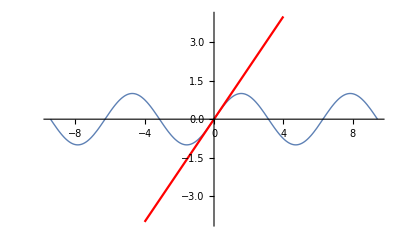
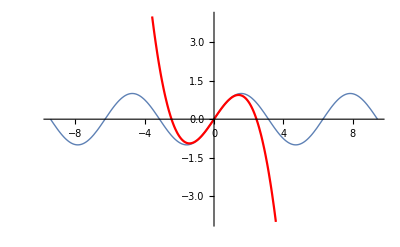
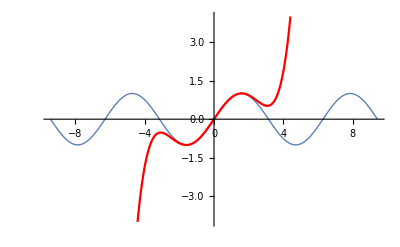
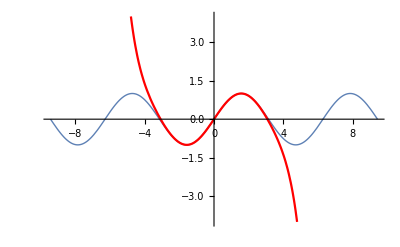
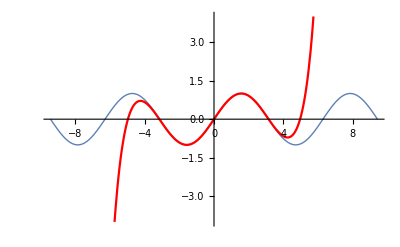
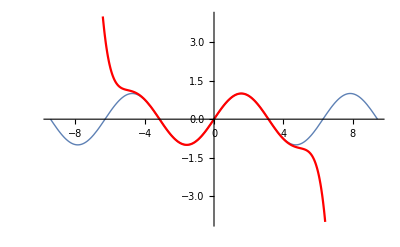
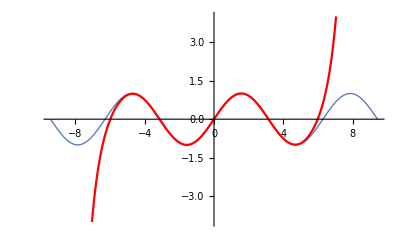
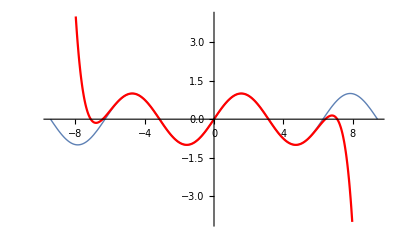

```mathematica
Table[Plot[{Sin[x],Evaluate[Normal[Series[Sin[x],{x,0,2m}]]]},{x,-3Pi,3Pi},PlotRange->{-4,4},PlotStyle->{Thick,Red}],{m,8}]
```

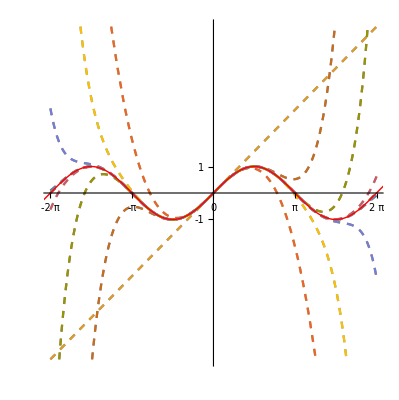

```mathematica
p1=Plot[Sin[x],{x,-3Pi,3Pi},PlotRange->{-3,3},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[Sin[x],{x,0,n}]],{n,20}]],{x,-2Pi,2Pi},AspectRatio->Automatic,PlotRange->{-2Pi,2Pi},PlotStyle->Dashed,Ticks->{{-2Pi,-Pi,0,Pi,2Pi},{-1,1}}];
Show[p2,p1]
```

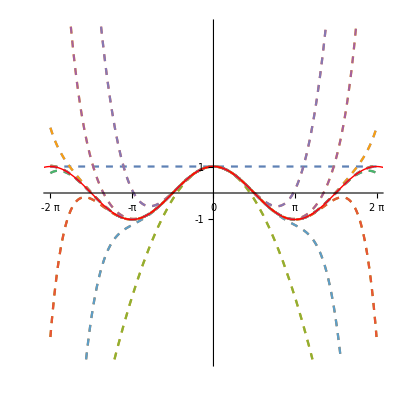

```mathematica
p1=Plot[Cos[x],{x,-3Pi,3Pi},PlotRange->{-4,4},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[Cos[x],{x,0,n}]],{n,20}]],{x,-2Pi,2Pi},AspectRatio->Automatic,PlotRange->{-2Pi,2Pi},PlotStyle->Dashed,Ticks->{{-2Pi,-Pi,0,Pi,2Pi},{-1,1}}];
Show[p2,p1]
```

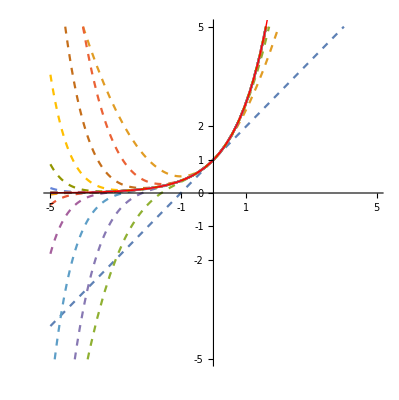

```mathematica
p1=Plot[E^x,{x,-5,5},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[E^x,{x,0,n}]],{n,20}]],{x,-5,5},AspectRatio->Automatic,PlotRange->{-5,5},PlotStyle->Dashed,Ticks->{{-5,-2,-1,0,1,2,5}}];
Show[p2,p1]
```

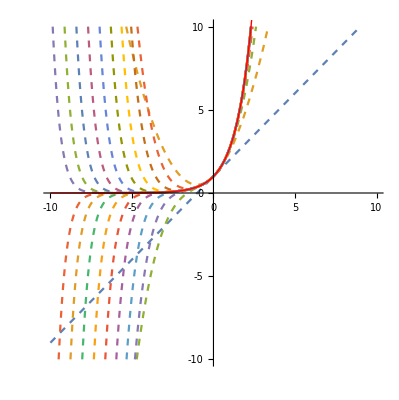

```mathematica
p1=Plot[E^x,{x,-10,10},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[E^x,{x,0,n}]],{n,20}]],{x,-10,10},AspectRatio->Automatic,PlotRange->{-10,10},PlotStyle->Dashed,Ticks->{{-10,-5,0,5,10}}];
Show[p2,p1]
```

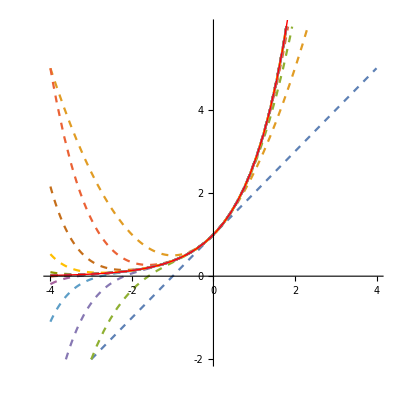

```mathematica
p1=Plot[E^x,{x,-4,4},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[E^x,{x,0,n}]],{n,20}]],{x,-4,4},AspectRatio->Automatic,PlotRange->{-2,6},PlotStyle->Dashed,Ticks->{{-4,-2,0,2,4}}];
Show[p2,p1]
```

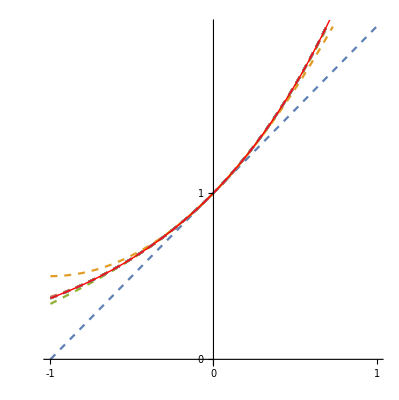

```mathematica
p1=Plot[E^x,{x,-1,1},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[E^x,{x,0,n}]],{n,20}]],{x,-1,1},AspectRatio->Automatic,PlotRange->{0,2},PlotStyle->Dashed,Ticks->{{-1,0,1}}];
Show[p2,p1]
```

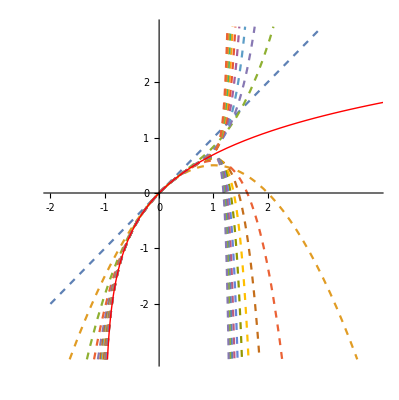

```mathematica
p1=Plot[Log[x+1],{x,-3,5},PlotRange->{-3,3},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[Log[x+1],{x,0,n}]],{n,20}]],{x,-2,4},AspectRatio->Automatic,PlotRange->{-3,3},PlotStyle->Dashed,Ticks->{{-2,-1,0,1,2}}];
p3=ContourPlot[{x==1,x==-1},{x,-2,2},{y,-4,4},ContourStyle->{{Dashed,Gray},{Dashed,Gray}}];
Show[p2,p1]
```

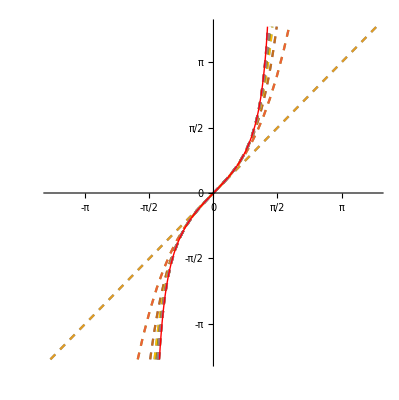

```mathematica
p1=Plot[Tan[x],{x,-Pi/2,Pi/2},PlotRange->{-4,4},PlotStyle->{Thick,Red},Exclusions->{-Pi/2,Pi/2}];
p2=Plot[Evaluate[Table[Normal[Series[Tan[x],{x,0,n}]],{n,20}]],{x,-4,4},AspectRatio->Automatic,PlotRange->{-4,4},PlotStyle->Dashed,Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi}}];
Show[p2,p1]
```

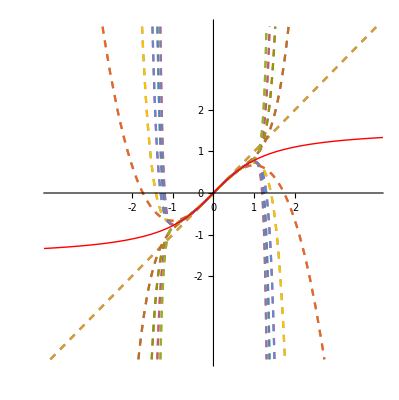

```mathematica
p1=Plot[ArcTan[x],{x,-5,5},PlotRange->{-4,4},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[ArcTan[x],{x,0,n}]],{n,20}]],{x,-4,4},AspectRatio->Automatic,PlotRange->{-4,4},PlotStyle->Dashed,Ticks->{{-2,-1,0,1,2}}];
Show[p2,p1]
```

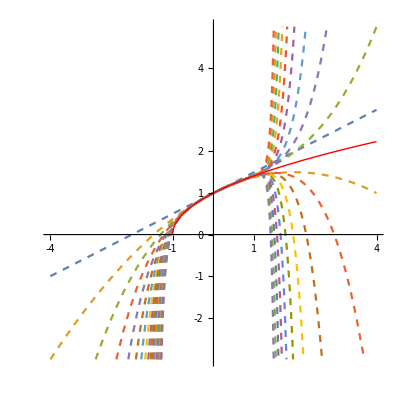

```mathematica
p1=Plot[(1+x)^{1/2},{x,-2,4},PlotRange->{-4,4},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[(1+x)^{1/2},{x,0,n}]],{n,20}]],{x,-4,4},AspectRatio->Automatic,PlotRange->{-3,5},PlotStyle->Dashed,Ticks->{{-4,-2,-1,0,1,2,4}}];
Show[p2,p1]
```

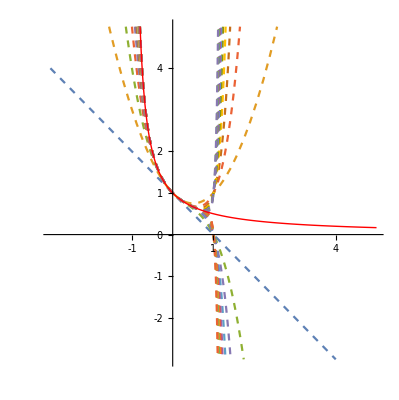

```mathematica
p1=Plot[(1+x)^{-1},{x,-0.99,5},PlotRange->{-3,5},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[(1+x)^{-1},{x,0,n}]],{n,20}]],{x,-3,5},AspectRatio->Automatic,PlotRange->{-3,5},PlotStyle->Dashed,Ticks->{{-4,-2,-1,0,1,2,4}}];
Show[p2,p1]
```

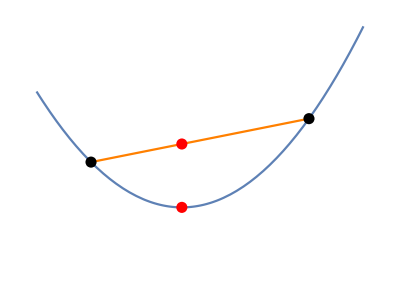

```mathematica
f=Function[x,x^2-2x+1.3];
k=(f[1.7]-f[0.5])/1.2;
p1=Plot[f[x],{x,0.2,2},AxesOrigin->{0.3,0},AspectRatio->Automatic,Epilog->{Disk[{0.5,f[0.5]},Offset[4]],Disk[{1.7,f[1.7]},Offset[4]],
Red,Disk[{1,f[1]},Offset[4]],Disk[{1,k(1-0.5)+f[0.5]},Offset[4]]},Axes->False];
p2=Plot[k(x-0.5)+f[0.5],{x,0.5,1.7},PlotStyle->{Orange}];
p3=ContourPlot[x==0.5,{x,0,1},{y,0,f[0.5]},ContourStyle->{Gray,Dashed}];
p4=ContourPlot[x==1.7,{x,1,2},{y,0,f[1.7]},ContourStyle->{Gray,Dashed}];
p5=ContourPlot[x==1,{x,0,2},{y,0,k(1-0.5)+f[0.5]},ContourStyle->{Green,Dashed}];
Show[p1,p2]
```

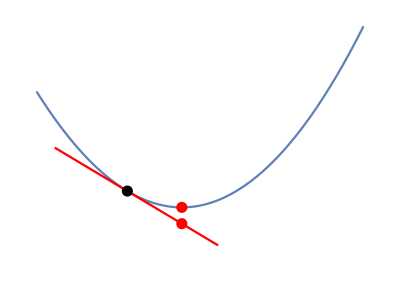

```mathematica
f=Function[x,x^2-2x+1.3];
df=Function[x,D[f[x],x]];
k=(f[1.7]-f[0.7])/1;
k1=df[x]/.x-> 0.7;
p1=Plot[f[x],{x,0.2,2},AxesOrigin->{0.3,0},AspectRatio->Automatic,Epilog->{Disk[{0.7,f[0.7]},Offset[4]],
Red,Disk[{1,f[1]},Offset[4]],Disk[{1,k1(1-0.7)+f[0.7]},Offset[4]]},Axes->False];
p2=Plot[k(x-0.7)+f[0.7],{x,0.7,1.7},PlotStyle->{Orange}];
p3=ContourPlot[x==0.7,{x,0,1},{y,0,f[0.7]},ContourStyle->{Gray,Dashed}];
p4=ContourPlot[x==1.7,{x,1,2},{y,0,f[1.7]},ContourStyle->{Gray,Dashed}];
p5=ContourPlot[x==1,{x,0,2},{y,0,k(1-0.7)+f[0.7]},ContourStyle->{Green,Dashed}];
p6=Plot[k1(x-0.7)+f[0.7],{x,0.3,1.2},PlotStyle->{Red}];
Show[p1,p6]
```

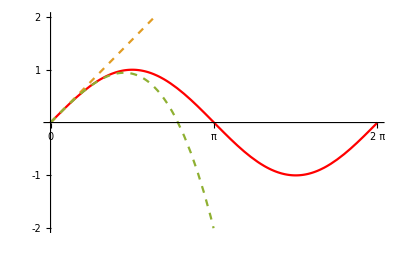

```mathematica
Plot[{Sin[x],x,x-x^3/6},{x,0,2Pi},PlotStyle->{Red,Dashed,Dashed},PlotRange->{-2,2},AspectRatio->Automatic,Ticks->{{-2Pi,-Pi,0,Pi,2Pi},{-4,-2,-1,1,2,4}}]
```

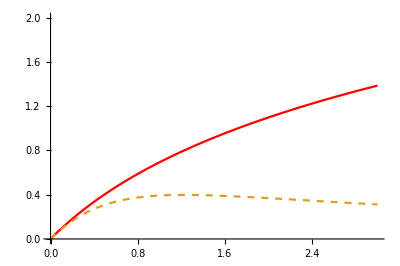

```mathematica
Plot[{Log[1+x],ArcTan[x]/(1+x)},{x,0,3},PlotStyle->{Red,Dashed,Dashed},PlotRange->{-0,2},AspectRatio->Automatic]
```

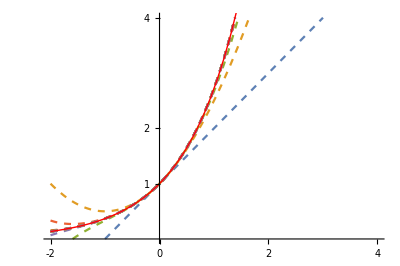

```mathematica
p1=Plot[E^x,{x,-2,4},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[E^x,{x,0,n}]],{n,20}]],{x,-2,4},AspectRatio->Automatic,PlotRange->{0,4},PlotStyle->Dashed,Ticks->{{-2,0,2,4},{1,2,4}}];
Show[p2,p1]
```

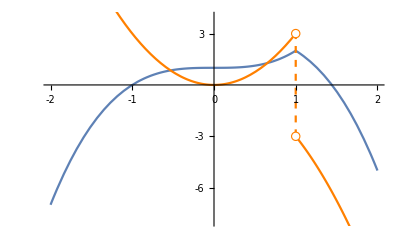

```mathematica
f1=Function[x,2-Abs[x^3-1]];
p1=Plot[f1[x],{x,-2,2},PlotRange->{-8,4},Epilog->{White,EdgeForm[Orange],Disk[{1,3},Offset[3]],Disk[{1,-3},Offset[3]]},Ticks->{{-2,-1,0,1,2},{-6,-3,3}}];
p2=Plot[3x^2,{x,-2,1},PlotStyle->{Orange}];
p3=Plot[-3x^2,{x,1,2},PlotStyle->{Orange}];
p4=ContourPlot[x==1,{x,0,2},{y,-3,3},ContourStyle->{Orange,Dashed}];
Show[p1,p2,p3,p4]
```

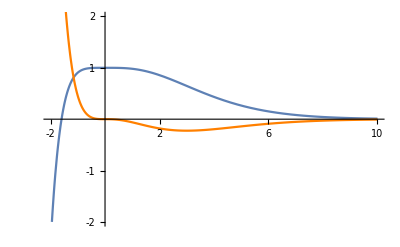

```mathematica
f2=Function[x,(1+x+x^2/2+x^3/6)E^(-x)];
df2=Function[x,-x^3/6*E^(-x)];
p1=Plot[f2[x],{x,-2,10},PlotRange->{-2,2},Ticks->{{-2,0,2,4,6,8,10},{-2,-1,1,2}}];
p2=Plot[df2[x],{x,-4,10},PlotStyle->{Orange}];
Show[p1,p2]
```

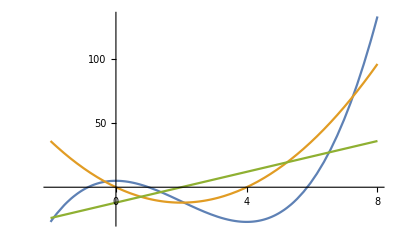

```mathematica
f3=Function[x,x^3-6x^2+5];
df3=Function[x,3x^2-12x];
ddf3=Function[x,6x-12];
Plot[{f3[x],df3[x],ddf3[x]},{x,-2,8},Ticks->{{-4,-2,0,2,4,6,8,10},{-150,-100,-50,50,100,150}}]
```

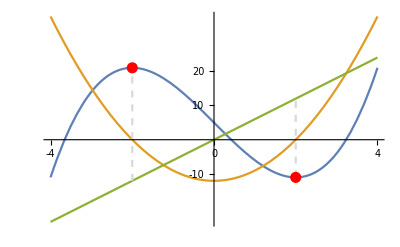

```mathematica
f3=Function[x,x^3-12x+5];
df3=Function[x,3x^2-12];
ddf3=Function[x,6x];
p1=Plot[{f3[x],df3[x],ddf3[x]},{x,-4,4},Ticks->{{-4,-2,0,2,4,6,8,10},{-10,10,20,40}},Epilog->{Red,Disk[{-2,f3[-2]},Offset[4]],Disk[{2,f3[2]},Offset[4]]}];
p2=ContourPlot[{x==-2},{x,-3,-1},{y,ddf3[-2],f3[-2]},ContourStyle->{LightGray,Dashed}];
p3=ContourPlot[{x==2},{x,1,3},{y,f3[2],ddf3[2]},ContourStyle->{LightGray,Dashed}];
Show[p1,p2,p3]
```

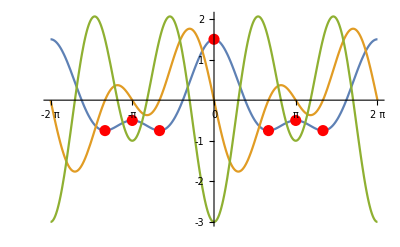

```mathematica
f4=Function[x,Cos[x]+Cos[2x]/2];
df4=Function[x,-Sin[x]-Sin[2x]];
ddf4=Function[x,-Cos[x]-2Cos[2x]];
Plot[{f4[x],df4[x],ddf4[x]},{x,-2Pi,2Pi},Ticks->{{-2Pi,-Pi,0,Pi,2Pi},{-3,-2,-1,1,2}},Epilog->{Red,Disk[{0,f4[0]},Offset[4]],Disk[{Pi,f4[Pi]},Offset[4]],Disk[{-Pi,f4[-Pi]},Offset[4]],Disk[{2Pi/3,f4[2Pi/3]},Offset[4]],Disk[{4Pi/3,f4[4Pi/3]},Offset[4]],Disk[{-2Pi/3,f4[-2Pi/3]},Offset[4]],Disk[{-4Pi/3,f4[-4Pi/3]},Offset[4]]}]
```

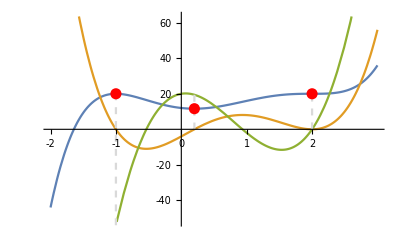

```mathematica
f6=Function[x,(x+1)^2(x-2)^3+20];
df6=Function[x,2(x+1)(x-2)^3+3(x+1)^2(x-2)^2];
ddf6=Function[x,2(x-2)^3+12(x+1)(x-2)^2+6(x+1)^2(x-2)];
p1=Plot[{f6[x],df6[x],ddf6[x]},{x,-2,3},Epilog->{Red,Disk[{-1,f6[-1]},Offset[4]],Disk[{0.2,f6[0.2]},Offset[4]],Disk[{2,f6[2]},Offset[4]]},Ticks->{{-2,-1,0,1,2},{-40,-20,20,40,60}}];
p2=ContourPlot[x==-1,{x,-2,0},{y,ddf6[-1],f6[-1]},ContourStyle->{LightGray,Dashed}];
p3=ContourPlot[x==0.2,{x,0,1},{y,df6[0.2],ddf6[0.2]},ContourStyle->{LightGray,Dashed}];
p4=ContourPlot[x==2,{x,1,3},{y,df6[2],f6[2]},ContourStyle->{LightGray,Dashed}];
Show[p1,p2,p3,p4]
```

```mathematica
Expand[(x+1)^2(x-2)^3+20]
```

12-4 x+10 x^2+x^3-4 x^4+x^5

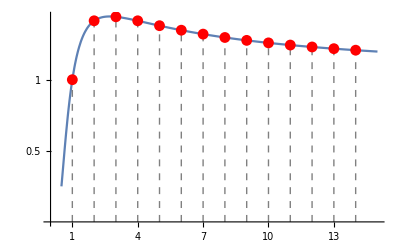

```mathematica
p1=Plot[x^(1/x),{x,0.5,15},AxesOrigin->{0,0},Ticks->{{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{0.5,1,1.5}}];
p2=ListPlot[Table[n^(1/n),{n,14}],PlotStyle->Red,Filling->0,FillingStyle->Directive[Gray,Dashed]];
Show[p1,p2]
```

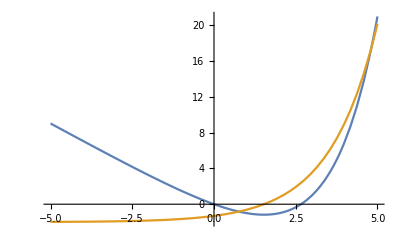

```mathematica
Clear[f];
f[x_]=2^x-2x-1;
Plot[{f[x],f'[x]},{x,-5,5}]
```

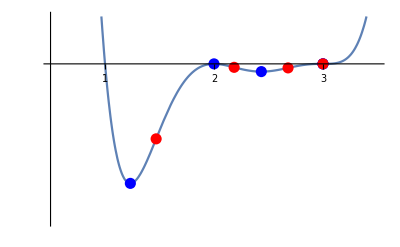

```mathematica
Clear[f];
f[x_]=(x-1)(x-2)^2(x-3)^3;
sp=Solve[f'[x]==0,x];
sp1=x/.sp[[1]];
sp2=x/.sp[[2]];
sp3=x/.sp[[3]];
sp4=x/.sp[[4]];
sp5=x/.sp[[5]];
sg=Solve[f''[x]==0,x];
sg1=x/.sg[[1]];
sg2=x/.sg[[2]];
sg3=x/.sg[[3]];
sg4=x/.sg[[4]];
Plot[f[x],{x,0.5,3.5},PlotRange->{-1,0.3},Epilog->{Blue,Disk[{sp1,f[sp1]},Offset[4]],Disk[{sp2,f[sp2]},Offset[4]],Disk[{sp3,f[sp3]},Offset[4]],Disk[{sp4,f[sp4]},Offset[4]],Disk[{sp5,f[sp5]},Offset[4]],Red,Disk[{sg1,f[sg1]},Offset[4]],Disk[{sg2,f[sg2]},Offset[4]],Disk[{sg3,f[sg3]},Offset[4]],Disk[{sg4,f[sg4]},Offset[4]]},Ticks->{{1,2,3}}]
```

```mathematica
Solve[f''[x]==0,x]
```

{{x→3},{x→1/9 (19+10/(1/5 (-49+27 ⅈ √31))^(1/3)+(1/5 (-49+27 ⅈ √31))^(1/3))},{x→19/9-(5 (1+ⅈ √3))/(9 (1/5 (-49+27 ⅈ √31))^(1/3))-1/18 (1-ⅈ √3) (1/5 (-49+27 ⅈ √31))^(1/3)},{x→19/9-(5 (1-ⅈ √3))/(9 (1/5 (-49+27 ⅈ √31))^(1/3))-1/18 (1+ⅈ √3) (1/5 (-49+27 ⅈ √31))^(1/3)}}

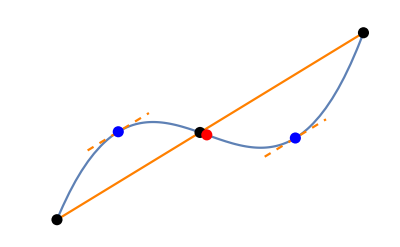

```mathematica
Clear[f];
a=0.2;
b=3.2;
f[x_]=(x-1)(x-2)(x-3)+(x-1)(x-2.5);
k=(f[b]-f[a])/(b-a);
Clear[l];
l[x_]=k*(x-a)+f[a];
ip=Solve[f[x]==l[x],x];
c=x/.ip[[2]];
sp=Solve[f'[x]==k,x];
sp1=x/.sp[[1]];
sp2=x/.sp[[2]];
gp=Solve[f''[x]==0,x];
d=x/.gp[[1]];
p1=Plot[f[x],{x,a,b},PlotRange->{-2.3,2.3},Epilog->{Disk[{a,f[a]},Offset[4]],Disk[{b,f[b]},Offset[4]],Disk[{c,f[c]},Offset[4]],Blue,
Disk[{sp1,f[sp1]},Offset[4]],Disk[{sp2,f[sp2]},Offset[4]],Red,Disk[{d,f[d]},Offset[4]]},Axes->False];
p2=Plot[l[x],{x,a,b},PlotStyle->{Orange}];
p3=Plot[k(x-sp1)+f[sp1],{x,sp1-0.3,sp1+0.3},PlotStyle->{Orange,Dashed}];
p4=Plot[k(x-sp2)+f[sp2],{x,sp2-0.3,sp2+0.3},PlotStyle->{Orange,Dashed}];
Show[p1,p2,p3,p4]
```

```mathematica
Solve[f[x]==l[x],x]
```

{{x→0.2},{x→1.6},{x→3.2}}

```mathematica
Solve[f''[x]==0,x]
```

{{x→5/3}}